```mathematica
(*Quit[]*)
```

```mathematica
ClearAll["Global`*"];
ClearAll[Evaluate[Context[]<>"*"]];
SetDirectory@NotebookDirectory[]
```

/run/media/bryan/Resources/Documents/Base/4. 实验/4. 闪烁谱仪/data

```mathematica
<<"~/apps/eclipse-workspace/MathUtils/MathUtils.m"
Information["Funcs`*"];
autoCollapse[];
```

Get::noopen: Cannot open ~/apps/eclipse-workspace/MathUtils/MathUtils.m.

$Failed

```mathematica
<<MaTeX`
SetOptions[MaTeX,"Preamble"->{"\\usepackage{physics,siunitx}"}];

omarker=Graphics[{Thickness[.2],Disk[]}];
({colors,colorsDefault}
=colorPalette/@{"Scientific","Default"})//Grid
```

RGBColor[0.9, 0.36, 0.054] | RGBColor[0.365248, 0.427802, 0.758297] | RGBColor[0.945109, 0.593901, 0.] | RGBColor[0.645957, 0.253192, 0.685109] | RGBColor[0.285821, 0.56, 0.450773] | RGBColor[0.7, 0.336, 0.] | RGBColor[0.491486, 0.345109, 0.8] | RGBColor[0.71788, 0.568653, 0.] | RGBColor[0.70743, 0.224, 0.542415] | RGBColor[0.287228, 0.490217, 0.664674] | RGBColor[0.982289285128704, 0.5771321368979874, 0.011542503255145636] | RGBColor[0.5876740325800278, 0.2877284499870081, 0.7500695697462922] | RGBColor[0.4262088601796793, 0.5581552810007578, 0.2777996730417023] | RGBColor[0.9431487543762861, 0.414555896337833, 0.07140829055870854] | RGBColor[0.41497437140121635, 0.393632147507352, 0.7842993779115092]
RGBColor[0.368417, 0.506779, 0.709798] | RGBColor[0.880722, 0.611041, 0.142051] | RGBColor[0.560181, 0.691569, 0.194885] | RGBColor[0.922526, 0.385626, 0.209179] | RGBColor[0.528488, 0.470624, 0.701351] | RGBColor[0.772079, 0.431554, 0.102387] | RGBColor[0.363898, 0.618501, 0.782349] | RGBColor[1, 0.75, 0] | RGBColor[0.647624, 0.37816, 0.614037] | RGBColor[0.571589, 0.586483, 0.] | RGBColor[0.915, 0.3325, 0.2125] | RGBColor[0.40082222609352647, 0.5220066643438841, 0.85] | RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142] | RGBColor[0.736782672705901, 0.358, 0.5030266573755369] | RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]

```mathematica
sheet=Import["data.ods"];
spectrum=sheet⟦1⟧;
```

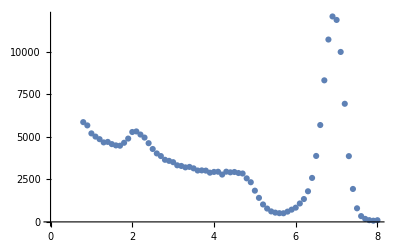

```mathematica
Import["data.ods"]⟦1⟧//ListPlot
```

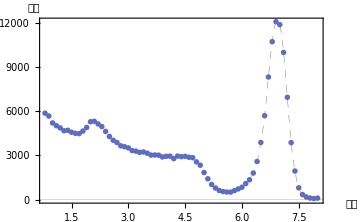

plots/spectrumPlot.pdf

```mathematica
spectrumPlot=Show[
ListPlot[spectrum
,PlotTheme->"Scientific"
,PlotStyle->colors⟦2⟧
,PlotRangeClipping->False

,PlotRange->{All,{0,All}}
,PlotRangePadding->{Automatic,
{0,.1*Max[spectrum⟦All,2⟧]}
}

,ImagePadding->{{42,54},{20,25}}
,Epilog->Join[
(Inset[Evaluate@Style[#1
,FontFamily->"黑体"
,FontSize->10.5],#2]&)@@@{
{Row@{"阈值",MaTeX["/\\,\\si{\\V}"]},Scaled[{1.1,0}]},
{"计数",Scaled[{-.02,1.06}]}
},{(*ADD EPILOGS HERE*)}
]
],
ListLinePlot[spectrum//Select[#⟦1⟧>6&]
,InterpolationOrder->3
,PlotStyle->Directive[
Thickness[.001],Dashing[.015],Gray
]
]
];
Magnify[spectrumPlot,2]
exportPlot[spectrumPlot]
```

```mathematica
highPeak
```

InterpolatingFunction[…]

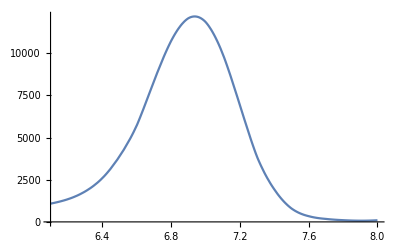

InterpolatingFunction::dmval: Input value {1.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{12175.5,{x→6.93763}}

```mathematica
highPeak=spectrum//Select[#⟦1⟧>6&]//Interpolation;
Plot[highPeak[x],{x,6.1,8.}]
FindMaximum[highPeak[x],x]
```

```mathematica
roots=FindRoot[highPeak[x]==12175.480931985727/2,{x,#}]&/@{6.2,7.1}
roots⟦All,1,2⟧//#⟦2⟧-#⟦1⟧&//#/6.937634030173124&
```

{{x→6.61629},{x→7.22613}}

0.087903

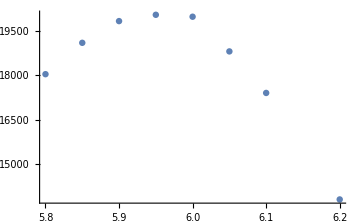
-Graphics-
{{4,20043}}

```mathematica
Column@{
ListPlot[sheet⟦#⟧,PlotRange->All,ImageSize->Medium],
Reverse[sheet⟦#⟧]⟦All,2⟧//FindPeaks
}&[5]
```

```mathematica
peaks={{.184,1.05},
{.662,3.56},
{1.17,5.95},
{1.33,6.78}};
peaks//TableForm
```

0.184 | 1.05
0.662 | 3.56
1.17 | 5.95
1.33 | 6.78

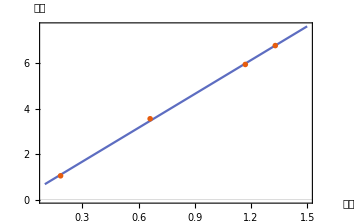

plots/linearModel.pdf

```mathematica
model=LinearModelFit[peaks,x,x];
linearModel=Show[
Plot[model[x]
,{x,.1,1.5}
,PlotTheme->"Scientific"
,PlotStyle->colors⟦2⟧
],
ListPlot[
peaks
,PlotStyle->Directive[
colors⟦1⟧
]
,PlotMarkers->{omarker,.025}
],ImageSize->Medium
,Epilog->Join[
(Inset[Evaluate@Style[#1
,FontFamily->"黑体"
,FontSize->10.5],#2]&)@@@{
{Row@{"能量",MaTeX["/\\,\\si{\\MeV}"]},Scaled[{1.135,0}]},
{Row@{"阈值",MaTeX["/\\,\\si{\\V}"]},Scaled[{0.,1.085}]}
},{(*ADD EPILOGS HERE*)}
]
,PlotRangeClipping->False
,ImagePadding->{{40,67.5},{20,30}}
]
exportPlot[linearModel]
```

```mathematica
Solve[model[x]==y,x]//Simplify
```

{{x→-0.0371675+0.201538 y}}

```mathematica
model[{"BestFitParameters","ParameterErrors"}]//TableForm
```

0.184419 | 4.96184
0.082033 | 0.0863517

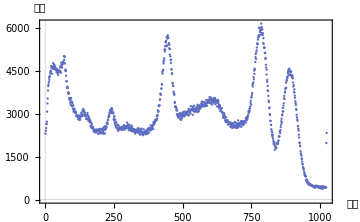
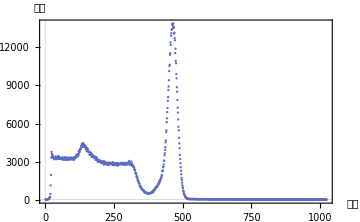

```mathematica
{mixedSpectrum,csSpectrum}=ListPlot[
Import[#,"CSV"]//Flatten,
PlotRange->All,
PlotTheme->"Scientific",
PlotStyle->colors⟦2⟧,
Epilog->Join[
(Inset[Evaluate@Style[#1
,FontFamily->"黑体"
,FontSize->10.5],#2]&)@@@{
{"道址",Scaled[{1.07,0}]},
{"计数",Scaled[{0.,1.07}]}
},{(*ADD EPILOGS HERE*)}
]
,PlotRangeClipping->False
,ImagePadding->{{40,42},{20,25}}
,ImageSize->Medium
]&/@{"raw/co_cs.csv","raw/cs.csv"}
```

```mathematica
(*exportPlot[mixedSpectrum]*)
```

plots/mixedSpectrum.pdf

```mathematica
(*exportPlot[csSpectrum]*)
```

plots/csSpectrum.pdf

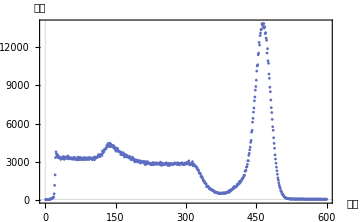

```mathematica
csSpectrumTruncated=ListPlot[
Import["raw/cs.csv","CSV"]
//Flatten//Part[#,;;600]&,
PlotRange->All,
PlotTheme->"Scientific",
PlotStyle->colors⟦2⟧,
Epilog->Join[
(Inset[Evaluate@Style[#1
,FontFamily->"黑体"
,FontSize->10.5],#2]&)@@@{
{"道址",Scaled[{1.07,0}]},
{"计数",Scaled[{0.,1.07}]}
},{(*ADD EPILOGS HERE*)}
]
,PlotRangeClipping->False
,ImagePadding->{{40,42},{20,25}}
,ImageSize->Medium
]
```

```mathematica
exportPlot[csSpectrumTruncated]
```

plots/csSpectrumTruncated.pdf